1.5

AiryAi[1.5 x^(2/3)]/x^(1/3)

AiryAiPrime[1.5 x^(2/3)]/x^(5/3)

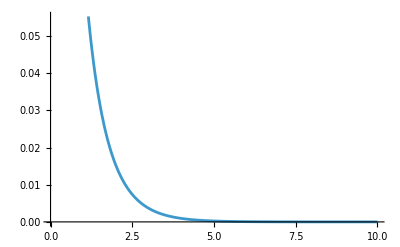

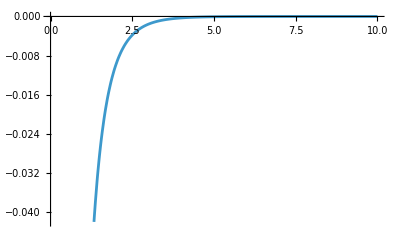

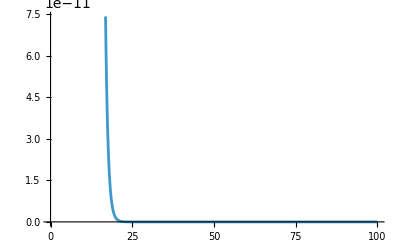

```mathematica
ζ=1.5
f[x_]=AiryAi[x^(2/3)*ζ]/x^(1/3)
g[x_]= AiryAiPrime[x^(2/3)*ζ]/x^(5/3)
Plot[f[x],{x,0,10}]
Plot[g[x],{x,0,10}]
Plot[f[x]-g[x],{x,0,100}]
```

```mathematica
(*Airy Integral Thing for V(r)=g/r^3*)
zetap[z_]=-(3/2(Sqrt[z^2-1]-ArcSec[z]))^(2/3);
zetam[z_]=(3/2(Log[(1+Sqrt[1-z^2])/z]-Sqrt[1-z^2]))^(2/3);
zeta[z_?NumericQ]:=Piecewise[{{((3/2)*(Log[(1+Sqrt[1-z^2])/z]-Sqrt[1-z^2]))^(2/3),0<z<1},{-((3/2)*(Sqrt[z^2-1]-ArcSec[z]))^(2/3),z>1}}];
phi[z_?NumericQ]:=(4 zeta[z]/(1-z^2))^(1/4);
integrand[z_?NumericQ,mu_?NumericQ]:=(phi[z]^2/z^2)*AiryAi[mu^(2/3)*zeta[z]]^2;
```

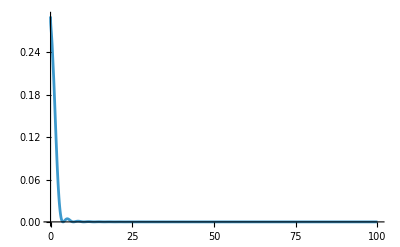

3.41382×10^-89

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {57.880172182366208522358110268073258078853606514346}. NIntegrate obtained 0.12700445320754973452879810847137839204841034312404 and 3.04632590936122487134962203062532459037306790793×10^-6 for the integral and error estimates.

0.00025404257692645841413642258984278288815781788582378

```mathematica
Plot[integrand[z,1],{z,0,100},PlotRange->All]
integrand[0.00001,10]
VllMu[mu_?NumericQ,g_:1]:=Module[{core,tail},core=NIntegrate[integrand[z,mu],{z,0,1},Exclusions->{z==1},WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
tail=NIntegrate[integrand[z,mu],{z,1,Infinity},Exclusions->{z==1},WorkingPrecision->50,AccuracyGoal->22,PrecisionGoal->22,Method->{"ExtrapolatingOscillatory"}];
g*mu^(-5/3)/(4π)*(core+tail)]; (*Does core + tail differenly to handly numerics better for each case*)
VllMu[10]
```

```mathematica
ClearAll[zetaBelow,zetaAbove,coreIntegrand,tailIntegrand,VllMuStable];

(*0<z<1 side:v=Sqrt[1-z^2] in (0,1)*)
zetaBelow[v_?NumericQ]:=((3/2)*(Log[(1+v)/Sqrt[1-v^2]]-v))^(2/3);

(*z>1 side:u=Sqrt[z^2-1] in (0,∞);arcsec z=arctan u*)
zetaAbove[u_?NumericQ]:=((3/2)*(u-ArcTan[u]))^(2/3);

coreIntegrand[v_?NumericQ,mu_?NumericQ]:=(2*Sqrt[zetaBelow[v]]/(1-v^2)^(3/2))*AiryAi[mu^(2/3)*zetaBelow[v]]^2;

tailIntegrand[u_?NumericQ,mu_?NumericQ]:=(2*Sqrt[zetaAbove[u]]/(1+u^2)^(3/2))*AiryAi[-mu^(2/3)*zetaAbove[u]]^2;

VllMuStable[mu_?NumericQ,g_:1]:=Module[{core,tail},core=NIntegrate[coreIntegrand[v,mu],{v,0,1},WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
tail=NIntegrate[tailIntegrand[u,mu],{u,0,Infinity},WorkingPrecision->50,AccuracyGoal->22,PrecisionGoal->22,Method->{"ExtrapolatingOscillatory"},MaxRecursion->20];
g*mu^(-5/3)/(4π)*(core+tail)];
(*VllMuStable[10]*)

(*Automatic large-mu extrapolation to get C0=lim_{mu->∞} mu^(7/3) V_l(k,k)/g*)AsymptoticC0[g_:1]:=Module[{mus,vals,x,fit,C0},mus=N@{40,55,70,90,120};(*chosen to be “large” but fast*)vals=Table[mu^(7/3)*VllMu[mu,g]/g,{mu,mus}];x=mus^(-4/3);fit=LinearModelFit[Transpose[{x,vals}],{1,ξ},ξ];;C0=fit[0]                 (*asymptotic constant*)];
AsymptoticC0[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {31.716538634385869737915700695672050858457302342848}. NIntegrate obtained 0.085444795031561982933039548885858168592716490764794 and 4.6196177917072769388739221468452480224586283387827×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {30.375394378947000016443047274943630300400911432775}. NIntegrate obtained 0.077585432686684006590041691747367472365244789318799 and 6.9323255826847546755818094383152242287910580132414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {15.515565434200121872226173211702273648770539705835}. NIntegrate obtained 0.072073698697250494384227721602380250951058271861426 and 0.000017921838162138278308173142086154445419808885440893 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.130725

```mathematica
ClearAll[zetaBelow,zetaTail,coreInt,tailInt,VllMuStable];

(*0<z<1 via v=Sqrt[1-z^2]∈(0,1)*)
zetaBelow[v_?NumericQ]:=((3/2)*(Log[(1+v)/Sqrt[1-v^2]]-v))^(2/3);

(*z>1 via u=Tan[t],t∈(0,π/2)*)
zetaTail[t_?NumericQ]:=((3/2)*(Tan[t]-t))^(2/3);

coreInt[v_?NumericQ,mu_?NumericQ]:=(2*Sqrt[zetaBelow[v]]/(1-v^2)^(3/2))*AiryAi[mu^(2/3)*zetaBelow[v]]^2;

tailInt[t_?NumericQ,mu_?NumericQ]:=Module[{zz=zetaTail[t]},2*Sqrt[zz]*Cos[t]*AiryAi[-mu^(2/3)*zz]^2];

VllMuStable[mu_?NumericQ,g_:1]:=Module[{core,tail},core=NIntegrate[coreInt[v,mu],{v,0,1},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,Method->{"LocalAdaptive","SymbolicProcessing"->0},MaxRecursion->20];
tail=NIntegrate[tailInt[t,mu],{t,0,Pi/2},WorkingPrecision->40,AccuracyGoal->18,PrecisionGoal->18,Method->{"LocalAdaptive","SymbolicProcessing"->0},MaxRecursion->30];
g*mu^(-5/3)*(core+tail)];
VllMuStable[10]
```

$Aborted

```mathematica
Integrate[(g/(2Pi^2))1/x *SphericalBesselJ[l,q*x]*SphericalBesselJ[l,p*x],{x,0,∞}]
```

ConditionalExpression[((q/p)^l Gamma[l] Hypergeometric2F1Regularized[-1/2,l,3/2+l,q^2/p^2])/(8 π^(3/2)), Re[l]>0&&q>0&&Re[p]>q&&p==Re[p]]

```mathematica
Integrate[1/x *Sqrt[Pi/(2p*x)]BesselJ[l+1/2,p*x]*Sqrt[Pi/(2q*x)]*BesselJ[l+1/2,q*x],{x,0,∞}]
```

ConditionalExpression[1/4 √(1/p) √π √(1/q) (q/p)^l √(p q) Gamma[l] Hypergeometric2F1Regularized[-1/2,l,3/2+l,q^2/p^2], Re[l]>0&&q>0&&Re[p]>q&&p==Re[p]]

```mathematica
Clear[a]
a[x_,l_,p_,q_]=1/x *Sqrt[Pi/(2p*x)]BesselJ[l+1/2,p*x]*Sqrt[Pi/(2q*x)]*BesselJ[l+1/2,q*x];
b[x_,l_,p_,q_]=1/x *SphericalBesselJ[l,q*x]*SphericalBesselJ[l,p*x];
Plot[a[x,1,2,3],{x,-10,10}];
Plot[b[x,1,2,3],{x,-10,10}];
```

(η^l Gamma[l] Hypergeometric2F1Regularized[-1/2,l,3/2+l,η^2])/(8 π^(3/2))

(η^l √(1-η^2))/(8 l^(3/2) π^(3/2))

1/(8 l^(3/2) π^(3/2))

1/(4 l (1+l) π^2)

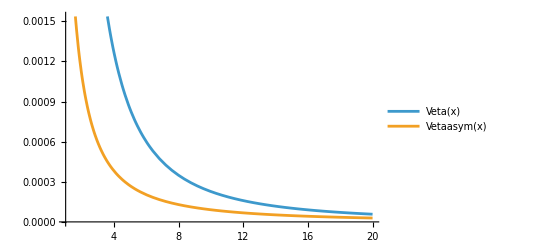

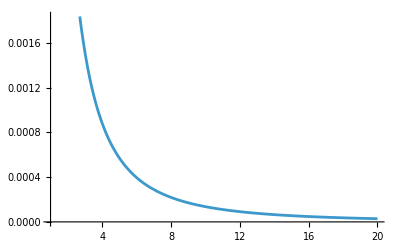

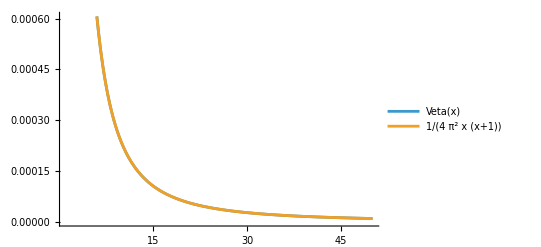

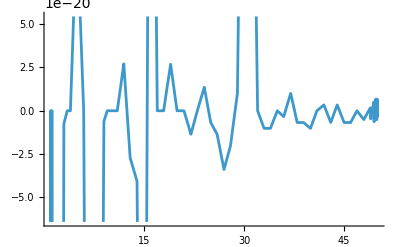

```mathematica
ηtest = 0.99;
Veta[η_,l_]=(g/(16Pi))*η^l*(Gamma[l]/Gamma[3/2])*Hypergeometric2F1Regularized[l,-1/2,l+3/2,η^2] 
Vetaasym[η_,l_]=(g/(8Pi^(3/2)))(1-η^2)^(1/2)η^l/(l^(3/2))
Vetaasymdiag[l_]=(g/(8Pi^(3/2)))*1/(l^(3/2))
Vetaasymdiag[l_]=(g/(4Pi^2))*1/(l(l+1))
Plot[{Veta[ηtest,x],Vetaasym[ηtest,x]},{x,1,20},PlotLegends->{HoldForm[Veta[x]],Vetaasym[x]}]
Plot[Veta[ηtest,x]-Vetaasym[ηtest,x],{x,1,20}]
Plot[{Veta[1,x],Vetaasymdiag[x]},{x,1,50},PlotLegends->{HoldForm[Veta[x]],Vetaasymdiag[x]}]
Plot[Veta[1,x]-Vetaasymdiag[x],{x,1,50}]
```

```mathematica
ftest[z_,l_]=(1-z)^(1/2)Hypergeometric2F1Regularized[3/2,-1/2,3/2+l,z/(z-1)]
ftestasym[z_,l_]=(1-z)^(1/2)Sqrt[l]/(Gamma[2+l])
```

√(1-z) Hypergeometric2F1Regularized[-1/2,3/2,3/2+l,z/(-1+z)]

(√l √(1-z))/Gamma[2+l]

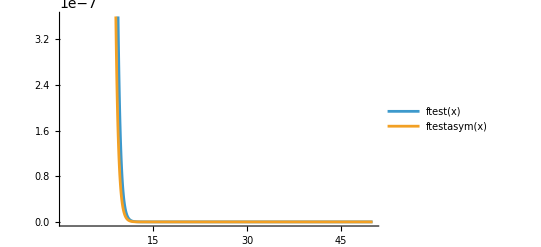

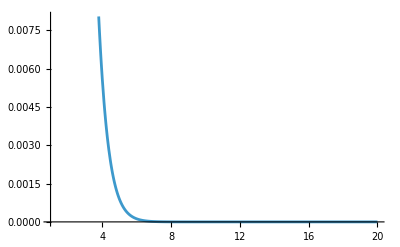

```mathematica
Plot[{ftest[0.1,x],ftestasym[0.8,x]},{x,1,50},PlotLegends->{HoldForm[ftest[x]],HoldForm[ftestasym[x]]}]
Plot[Abs[ftest[0.9,x]-ftestasym[0.9,x]],{x,1,20}]
```

```mathematica
Integrate[(g/(2Pi^2))1/x *SphericalBesselJ[l,p*x]*SphericalBesselJ[l,p*x],{x,0,∞}]
```

∫_0^∞ SphericalBesselJ[l,p x]^2/(2 π^2 x)ⅆx

```mathematica
Integrate[1^2/(1^2-x^2),{x,1-h,1+h},PrincipalValue->True]
```

ConditionalExpression[-ArcTanh[1-h]+ArcTanh[1/(1+h)], 0<Re[h]<1&&Im[h]==0]

```mathematica
Assuming[h∈Reals,Simplify[Series[-ArcTanh[1-h]+ArcTanh[1/(1+h)],{h,0,4}]]]
```

h/2+h^3/24+O[h]^5

```mathematica
Assuming[{l∈Reals},Integrate[x^2/(a^2-x^2)*Sqrt[1-(x/a)^2]*(x/a)^l,x]]
```

(x^3 (x/a)^l Hypergeometric2F1[1/2,(3+l)/2,(5+l)/2,x^2/a^2])/(a^2 (3+l))

```mathematica
Assuming[{l∈Reals,x>a},Integrate[x^2/(a^2-x^2)*Sqrt[1-(a/x)^2]*(a/x)^l,x]]
```

(√(1-a^2/x^2) (a/x)^l x^3 √(1-x^2/a^2) Hypergeometric2F1[1/2,1-l/2,2-l/2,x^2/a^2])/((-2+l) (-a^2+x^2))

```mathematica
Assuming[{l∈Reals,a/x<1},Integrate[a^4/(a^2x^2-x^4)*Sqrt[1-(a/x)^2]*(a/x)^l,x]]
```

(a^4 √(1-a^2/x^2) (a/x)^l √(1-x^2/a^2) Hypergeometric2F1[1/2,-1-l/2,-l/2,x^2/a^2])/((2+l) x (-a^2+x^2))

2

11.1

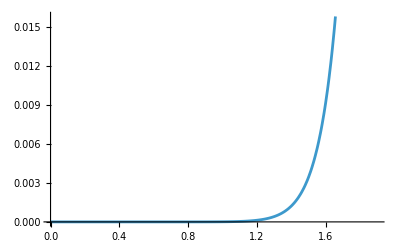

-Graphics-

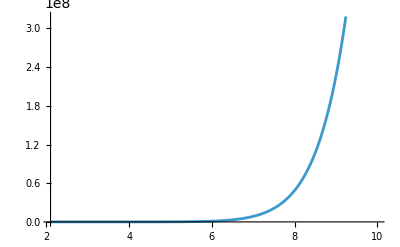

```mathematica
a=2
l=11.1
Plot[(x^3 (x/a)^l Hypergeometric2F1[1/2,(3+l)/2,(5+l)/2,x^2/a^2])/(a^2 (3+l)),{x,0,1.9}]
Plot[((a/x)^l x^2 Hypergeometric2F1[1/2,1-l/2,2-l/2,x^2/a^2])/((-2+l) a),{x,2.1,10}]
Plot[(a^3 (x/a)^l  Hypergeometric2F1[1/2,-1-l/2,-l/2,a^2/x^2])/((2+l) (a/x)^2),{x,2.1,10}]
Clear[a,l]
```

```mathematica
ClearAll;
a=2;
l=100;
δ=a/l;
Integrand[x_]=x^2/(a^2-x^2)*Sqrt[1-(x/a)^2]*(x/a)^l;
N[Integrate[Integrand[x],{x,0,a-δ}]]
Integrated[x_]=N[Integrate[Integrand[x],x]];
Integrated[a-δ]
N[Integrate[x^2/(a^2-x^2)*Sqrt[1-(a/x)^2]*(a/x)^l,{x,2.1,Infinity}]]
N[Integrate[a^4/(x^2(a^2-x^2))*Sqrt[1-(x/a)^2]*(x/a)^l,{x,0,a^2/2.1}]]
z[x_]:=x^2/(a^2-x^2)*Sqrt[1-(a/x)^2]*(a/x)^l;
c[x_]:=-a^4/(x^2(a^2-x^2))*Sqrt[1-(x/a)^2]*(x/a)^l;
ClearAll;
```

0.0374286

0.0374286

-0.00048818

0.00048818

ClearAll

```mathematica
Clear[a,l,g,z,c,δ,p]
f[ϵ_]=Assuming[l>1,Integrate[(1-(k/p)^2)(k/p)^(2l)*k^2/(p^2-k^2),{k,0,p-ϵ}]]
g[ϵ_]=Assuming[l>1,Integrate[(1-(p/k)^2)(p/k)^(2l)*k^2/(p^2-k^2),{k,p+ϵ,Infinity}]]
FullSimplify[f[ϵ]+g[ϵ]]
```

((p-ϵ)^3 (1-ϵ/p)^(2 l))/((3+2 l) p^2)

ConditionalExpression[-(p^(2 l) (p+ϵ)^(1-2 l))/(-1+2 l), ϵ+Re[p]>0&&p==Re[p]]

ConditionalExpression[(p^(2 l) (p+ϵ)^(1-2 l))/(1-2 l)+((p-ϵ)^3 (1-ϵ/p)^(2 l))/((3+2 l) p^2), ϵ+Re[p]>0&&p==Re[p]]